## Parameters

```mathematica
Vcont[r_]:=ccont-αcont/r+σcont r;
V[r_,α_,σ_,c_]:=c-α/r+σ r;
Vsb[r_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](c-α/r+σ r)+HeavisideTheta[r-1.25/0.197](c-α/(1.25/0.197)+σ 1.25/0.197);
Veff[r_,l_,m_]:=(l(l+1))/(2m r^2);
σcont=0.415^2;
ccont=-0.176696;
αcont=0.50425;
mc=1.47164;
mb=4.882;
mbe=0.041;
μc=mc/2;
μb=mb/2;
```

```mathematica
δ=1/100;
```

```mathematica
V[x Exp[ⅈ δ]]
```

-0.176696-(0.504225-0.00504242 ⅈ)/x+(0.172216+0.00172222 ⅈ) x

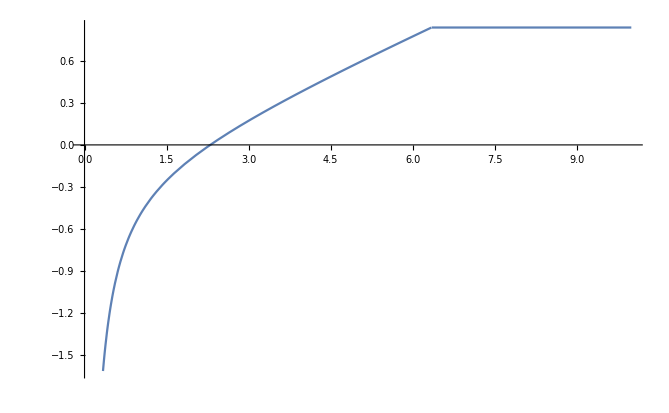

```mathematica
Plot[Vsb[r,αcont,σcont,ccont],{r,0,10}]
```

## Charmonium

### Swave

```mathematica
{ccsvals,ccsvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+Vcont[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

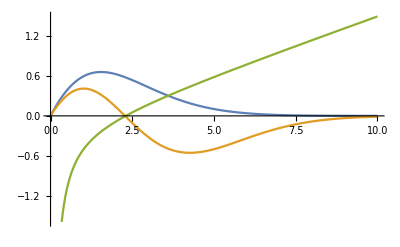

```mathematica
Plot[{ccsvecs[[1]][x],ccsvecs[[2]][x],Vcont[x]},{x,0,10}]
```

```mathematica
ccsvals
```

{0.152928,0.738566,1.16928,1.53686}

```mathematica
ccsmass=ConstantArray[2 mc,2]+Sort[ccsvals]
```

{3.09621,3.68185}

```mathematica
EMfactor=(ccsmass[[2]](ccsvecs[[1]][10^-100])/10^-100)^2/(ccsmass[[1]](ccsvecs[[2]][10^-100])/10^-100)^2
```

2.0689

```mathematica
{ccsvalsi,ccsvecsi}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]Exp[-2 ⅈ δ]+V[x Exp[ⅈ δ]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccsvalsi
```

{0.152928+1.11666×10^-12 ⅈ,0.738566+1.70776×10^-12 ⅈ,1.16928+3.01912×10^-12 ⅈ,1.53686+8.25092×10^-13 ⅈ}

### Pwave

```mathematica
{ccpvals,ccpvecs}=NDEigensystem[{-1/(2μc)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μc]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

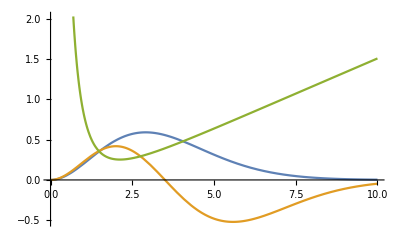

```mathematica
Plot[{ccpvecs[[1]][x],ccpvecs[[2]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
ccpmass=ConstantArray[2 mc,2]+Sort[ccpvals][[;;2]]
```

{3.50904,3.96034}

## Bottomonium

### Swave

```mathematica
{bbvals,bbvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

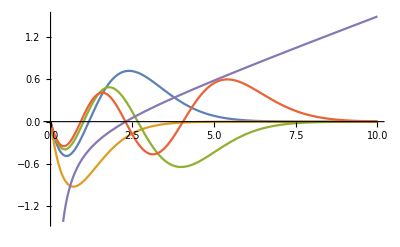

```mathematica
Plot[{bbvecs[[1]][x],bbvecs[[2]][x],bbvecs[[3]][x],bbvecs[[4]][x],V[x]},{x,0,10}]
```

```mathematica
bbmass=ConstantArray[2 mb,4]+Sort[bbvals][[;;4]]
```

{9.4599,10.019,10.3525,10.6217}

### Pwave

```mathematica
{bbpvals,bbpvecs}=NDEigensystem[{-1/(2μb)Laplacian[u[x],{x}]+V[x] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

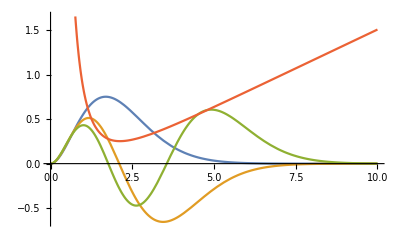

```mathematica
Plot[{bbpvecs[[1]][x],bbpvecs[[2]][x],bbpvecs[[3]][x],V[x]+Veff[x,1,μc]},{x,0,10}]
```

```mathematica
cbbpmass=ConstantArray[2 mb,3]+Sort[bbpvals]
```

{9.92524,10.2681,10.5432}

## New parameters

### Bottomonium Fit

```mathematica
Off[NDEigenvalues::femcnsd]
```

```mathematica
bbswavePDG={10.02326,9.4603,10.3552,10.5794};
bbswavePDGe={0.00031,0.00026,0.0002,0.0012};
bbswavePDG3={10.02326,9.4603,10.3552};
bbswavePDG3e={{10.02326,0.00031},{9.4603,0.00026},{10.3552,0.0002}};
bbpwavePDG={9.88814,10.252,10.534};
```

```mathematica
mbrand:=RandomVariate[NormalDistribution[mb,mbe]];
bbswavePDG3rand:={RandomVariate[NormalDistribution[bbswavePDG3e[[1,1]],bbswavePDG3e[[1,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[2,1]],bbswavePDG3e[[2,2]]]],RandomVariate[NormalDistribution[bbswavePDG3e[[3,1]],bbswavePDG3e[[3,2]]]]};
```

```mathematica
bbswavemass3rand[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/mbrand Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
res={{},{},{}};
SetSharedVariable[res];
Module[{al,sig,const},
ParallelDo[{al,sig,const}={α,σ,c}/.Quiet[FindRoot[bbswavePDG3rand==bbswavemass3rand[α,σ,c],{{α,αcont},{σ,σcont},{c,ccont}}]];
res[[1]]=Append[res[[1]],al];
res[[2]]=Append[res[[2]],sig];
res[[3]]=Append[res[[3]],const];,{i,1,1000}]]//AbsoluteTiming
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,766,5].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {22} assigned to KernelObject[1,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[1,local,<defunct>] resurrected as KernelObject[3,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,767,6].

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {23} assigned to KernelObject[2,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[4,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1070,6].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {29} assigned to KernelObject[4,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[4,local,<defunct>] resurrected as KernelObject[5,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

{21549.1,Null}

```mathematica
αfinal={Mean[res[[1]]],StandardDeviation[res[[1]]]}
σfinal={Mean[res[[2]]],StandardDeviation[res[[2]]]}
cfinal={Mean[res[[3]]],StandardDeviation[res[[3]]]}
```

{0.513712,0.0025122}

{0.169559,0.000876753}

{-0.159582,0.00247235}

```mathematica
res1={{},{},{}};
SetSharedVariable[res];
Module[{al,sig,const},
ParallelDo[{al,sig,const}={α,σ,c}/.Quiet[FindRoot[bbswavePDG3rand==bbswavemass3rand[α,σ,c],{{α,αcont},{σ,σcont},{c,ccont}}]];
res[[1]]=Append[res[[1]],al];
res[[2]]=Append[res[[2]],sig];
res[[3]]=Append[res[[3]],const];,{i,1,1000}]]//AbsoluteTiming
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1104,6].

Kernels::rdead: Subkernel connected through KernelObject[6,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {33} assigned to KernelObject[6,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[6,local,<defunct>] resurrected as KernelObject[7,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1055,5].

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {41} assigned to KernelObject[3,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[3,local,<defunct>] resurrected as KernelObject[8,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/Applications/Mathematica.app/Contents/MacOS/WolframKernel" -subkernel -noinit -wstp,1229,5].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[8,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {41} assigned to KernelObject[8,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[8,local,<defunct>] resurrected as KernelObject[9,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

{58787.2,Null}

```mathematica
αfinal1={Mean[res[[1]]],StandardDeviation[res[[1]]]}
σfinal1={Mean[res[[2]]],StandardDeviation[res[[2]]]}
cfinal1={Mean[res[[3]]],StandardDeviation[res[[3]]]}
```

{0.513719,0.00246668}

{0.169555,0.000858102}

{-0.159566,0.00247529}

```mathematica
αfinal={0.5137193759431391,0.0024666827878353577}; (*2k run*)
σfinal={0.16955497884544793,0.0008581023195660334};
cfinal={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
bbswavemass[α_,σ_,c_]:=2mb + NDEigenvalues[{-1/(2μb)Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
bbpwavemass[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/(2μb)Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x]+Veff[x,1,μb]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
bbswavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{10.0234,9.46054,10.3554,10.5954}

```mathematica
bbpwavemass[αfinal[[1]],σfinal[[1]],cfinal[[1]]]
```

{9.9315,10.2729,10.5396}

```mathematica
bbpwavePDG={9.88814,10.252,10.534};
```

```mathematica
bbswavemass3[α_,σ_,c_]:=2mb+NDEigenvalues[{-1/(2 μb)Laplacian[u[x],{x}]+Vsb[x,α,σ,c] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
{al,sig,const}={α,σ,c}/.FindRoot[bbswavePDG3==bbswavemass3[α,σ,c],{{α,αcont},{σ,σcont},{c,ccont}}]
```

{0.513661,0.169576,-0.159655}

```mathematica
bbswavemass[al,sig,const]-bbswavePDG
```

{-7.91545×10^-12,-1.29852×10^-12,-4.4551×10^-12,0.0155633}

```mathematica
(*diff[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[Join[bbswavePDG-bbswavemass[α,σ,c],bbpwavePDG-bbpwavemass[α,σ,c]]]
diffs13[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbswavePDG3-bbswavemass3[α,σ,c]];
diffsall[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbswavePDG-bbswavemass[α,σ,c]];
diffpall[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[bbpwavePDG-bbpwavemass[α,σ,c]];
diffcheck[α_?NumericQ,σ_?NumericQ,c_?NumericQ]:=Norm[Join[bbswavemass[αcont,σcont,ccont]-bbswavemass[α,σ,c],bbpwavemass[αcont,σcont,ccont]-bbpwavemass[α,σ,c]]]*)
```

```mathematica
(*FindMinimum[diff[α,σ,c],{{α,0.5,0.,1.},{σ,0.415^2,0.,1.0},{c,-0.17,-1.,0.}},Method->"PrincipalAxis"]*)
```

```mathematica
(*FindMinimum[diffcheck[α,σ,c],{{α,0.5,0.,1.},{σ,0.415^2,0.,1.0},{c,-0.17,-1.,0.}},Method->"PrincipalAxis"]*)
```

```mathematica
(*NMinimize[{diff[α,σ,c],0≤α≤1,0≤σ≤1,-1≤c≤0},{α,σ,c}]//AbsoluteTiming*)
```

### Charmonium Fit

```mathematica
ccswavePDG={{3.0969,0.000006},{3.686097,0.0000025}};
ccswavePDG1={3.0969};
```

```mathematica
ccswavemass1[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+V[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.000001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
FindRoot[ccswavemass1[m]==ccswavePDG1,{m,mc}]
```

NDEigenvalues::femcnmd: The PDE coefficient {{1/m}} does not evaluate to a numeric matrix of dimensions {1,1} at the coordinate {15.}.

General::stop: Further output of NDEigenvalues::femcnmd will be suppressed during this calculation.

{m→1.46898}

```mathematica
mcnew=1.4689783072176936;
```

```mathematica
ccswavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+V[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
ccpwavemass[m_]:=2m+NDEigenvalues[{-1/m Laplacian[u[x],{x}]+V[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x]+Veff[x,1,m/2]u[x],DirichletCondition[u[x]==0,True]},u,{x,0,30},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccswavemass[mcnew]
```

{3.0969,3.68027}

```mathematica
ccpwavemass[mcnew]
```

{3.50964,3.95769}

```mathematica
ccfinal=NDEigensystem[{-1/mcnew Laplacian[u[x],{x}]+V[x,αfinal[[1]],σfinal[[1]],cfinal[[1]]] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,50},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.000001}}},"Eigensystem"->{"Arnoldi"}}];
```

Part::partd: Part specification αfinal⟦1⟧ is longer than depth of object.

Part::partd: Part specification σfinal⟦1⟧ is longer than depth of object.

Part::partd: Part specification cfinal⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDEigensystem::femcnmd: The PDE coefficient {{1/mcnew}} does not evaluate to a numeric matrix of dimensions {1,1} at the coordinate {25.}.

General::stop: Further output of NDEigensystem::femcnmd will be suppressed during this calculation.

```mathematica
2mcnew +ccfinal[[1]]
```

{3.0969,3.68027}

```mathematica
EMfactor=((2mcnew +ccfinal[[1,2]]) (ccfinal[[2,1]][10^-100])/10^-100)^2/((2mcnew +ccfinal[[1,1]])(ccfinal[[2,2]][10^-100])/10^-100)^2
```

2.0844

```mathematica
(0.023/0.052)^-1
```

2.26087

```mathematica
((ccfinal[[2,1]][10^-100])/10^-100)^2
```

0.904724

```mathematica
((ccfinal[[2,2]][10^-100])/10^-100)^2
```

0.612971

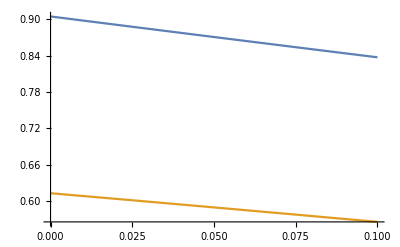

```mathematica
Plot[{((ccfinal[[2,1]][x])/x)^2,((ccfinal[[2,2]][x])/x)^2},{x,0,0.1}]
```